```mathematica
RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

293

293

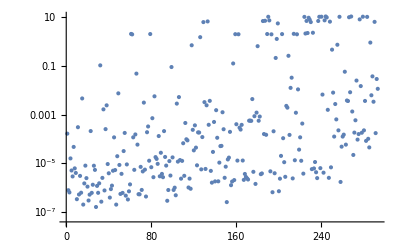

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False
]
```

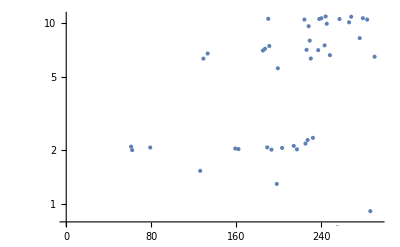

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0.8,All},
Joined->False
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|L0BPhaseSet→-7.88225,L1PhaseSet→-17.884,L2PhaseSet→-37.895,L3PhaseSet→10.9458,PDrive_mean_x→-0.0000621324,PDrive_mean_y→3.207×10^-7,PDrive_sigma_x→0.0000870669,PDrive_sigma_y→0.0000165489,PDrive_mean_xp→-0.00010041,PDrive_mean_yp→3.919×10^-7,PDrive_median_x→-0.0000154042,PDrive_median_y→6.782×10^-7,PDrive_median_xp→-0.0000852668,PDrive_median_yp→-3.516×10^-7,PDrive_sigmaSI90_x→0.0000705111,PDrive_sigmaSI90_y→0.000017433,PDrive_sigmaSI90_z→0.0000204213,PDrive_emitSI90_x→0.0000822561,PDrive_emitSI90_y→7.1884×10^-6,PDrive_zCentroid→991.332,PWitness_mean_x→-0.000475161,PWitness_mean_y→9.368×10^-7,PWitness_sigma_x→0.000100946,PWitness_sigma_y→0.0000212336,PWitness_mean_xp→-0.0000463115,PWitness_mean_yp→2.0831×10^-6,PWitness_median_x→-0.000498464,PWitness_median_y→7.474×10^-7,PWitness_median_xp→-0.0000561724,PWitness_median_yp→3.122×10^-7,PWitness_sigmaSI90_x→0.0000915352,PWitness_sigmaSI90_y→0.0000146341,PWitness_sigmaSI90_z→0.0000128243,PWitness_emitSI90_x→0.00005327,PWitness_emitSI90_y→4.5527×10^-6,PWitness_zCentroid→991.332,bunchSpacing→0.00019124,transverseCentroidOffset→0.000413029,lostChargeFraction→0.,errorTerm_lostChargeFraction→0.,errorTerm_bunchSpacing→0.,errorTerm_transverseOffset→0.,errorTerm_angleOffset→0.,errorTerm_mainObjective→0.554094,maximizeMe→10.8285|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L0BPhaseSet : -7.8822517794
L1PhaseSet : -17.8840129051
L2PhaseSet : -37.8949822755
L3PhaseSet : 10.9457635689
PDrive_mean_x : -0.0000621324
PDrive_mean_y : 3.207e-7
PDrive_sigma_x : 0.0000870669
PDrive_sigma_y : 0.0000165489
PDrive_mean_xp : -0.0001004097
PDrive_mean_yp : 3.919e-7
PDrive_median_x : -0.0000154042
PDrive_median_y : 6.782e-7
PDrive_median_xp : -0.0000852668
PDrive_median_yp : -3.516e-7
PDrive_sigmaSI90_x : 0.0000705111
PDrive_sigmaSI90_y : 0.000017433
PDrive_sigmaSI90_z : 0.0000204213
PDrive_emitSI90_x : 0.0000822561
PDrive_emitSI90_y : 7.1884e-6
PDrive_zCentroid : 991.3317148308
PWitness_mean_x : -0.0004751612
PWitness_mean_y : 9.368e-7
PWitness_sigma_x : 0.0001009461
PWitness_sigma_y : 0.0000212336
PWitness_mean_xp : -0.0000463115
PWitness_mean_yp : 2.0831e-6
PWitness_median_x : -0.0004984635
PWitness_median_y : 7.474e-7
PWitness_median_xp : -0.0000561724
PWitness_median_yp : 3.122e-7
PWitness_sigmaSI90_x : 0.0000915352
PWitness_sigmaSI90_y : 0.0000146341
PWitness_sigmaSI90_z : 0.0000128243
PWitness_emitSI90_x : 0.00005327
PWitness_emitSI90_y : 4.5527e-6
PWitness_zCentroid : 991.3319060709
bunchSpacing : 0.00019124
transverseCentroidOffset : 0.0004130293
lostChargeFraction : 0.
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0.
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 0.5540940248
maximizeMe : 10.8284871012

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

0.000413029

## Plot all

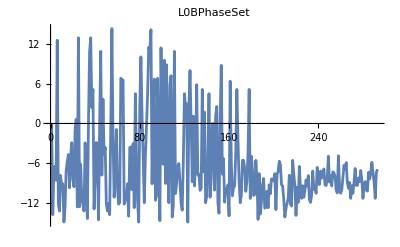
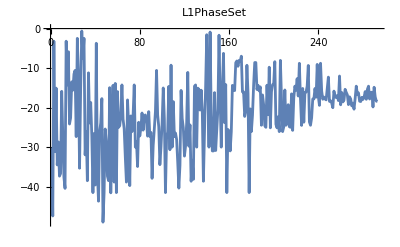
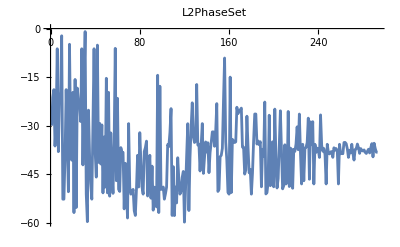
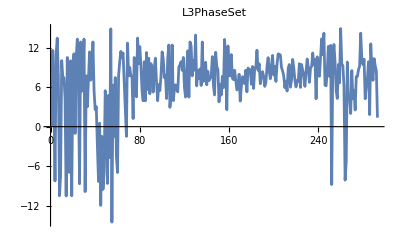
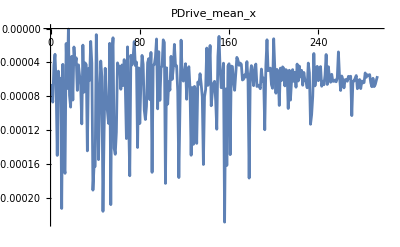
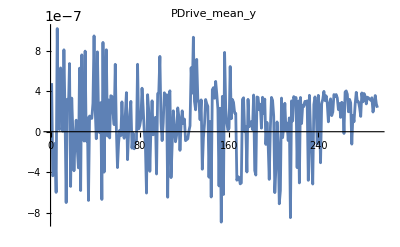
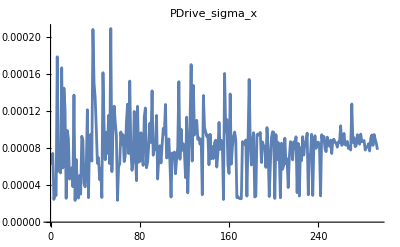
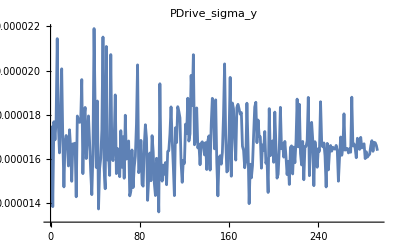
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0 | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L0BPhaseSet,L1PhaseSet,L2PhaseSet,L3PhaseSet}

```mathematica
fitVar = "PDrive_sigmaSI90_z"
```

PDrive_sigmaSI90_z

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

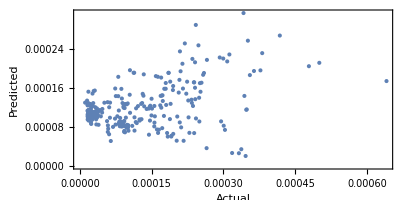

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
L0BPhaseSet | 1 | 3.43624×10^-8 | 3.43624×10^-8 | 3.68831 | 0.0557823
L1PhaseSet | 1 | 7.5013×10^-8 | 7.5013×10^-8 | 8.05159 | 0.0048693
L2PhaseSet | 1 | 4.12224×10^-7 | 4.12224×10^-7 | 44.2465 | 1.45421×10^-10
L3PhaseSet | 1 | 5.31948×10^-8 | 5.31948×10^-8 | 5.70971 | 0.0175146
Error | 288 | 2.68317×10^-6 | 9.31655×10^-9 |  | 
Total | 292 | 3.25796×10^-6 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | -7.88225 | -6.16122
L1PhaseSet | -20.312 | -17.884 | 2.42803
L2PhaseSet | -38.6737 | -37.895 | 0.778723
L3PhaseSet | -1.46329 | 10.9458 | 12.4091
S1EL_xOffset | 0.000385255 | Missing[KeyAbsent,S1EL_xOffset] | -0.000385255+Missing[KeyAbsent,S1EL_xOffset]
S1EL_yOffset | -0.000241114 | Missing[KeyAbsent,S1EL_yOffset] | 0.000241114+Missing[KeyAbsent,S1EL_yOffset]
S2EL_xOffset | -0.00141787 | Missing[KeyAbsent,S2EL_xOffset] | 0.00141787+Missing[KeyAbsent,S2EL_xOffset]
S2EL_yOffset | 0.0000111705 | Missing[KeyAbsent,S2EL_yOffset] | -0.0000111705+Missing[KeyAbsent,S2EL_yOffset]
S2ER_xOffset | -0.00223816 | Missing[KeyAbsent,S2ER_xOffset] | 0.00223816+Missing[KeyAbsent,S2ER_xOffset]
S2ER_yOffset | -0.000675996 | Missing[KeyAbsent,S2ER_yOffset] | 0.000675996+Missing[KeyAbsent,S2ER_yOffset]
S1ER_xOffset | 0.00100714 | Missing[KeyAbsent,S1ER_xOffset] | -0.00100714+Missing[KeyAbsent,S1ER_xOffset]
S1ER_yOffset | 0.000398456 | Missing[KeyAbsent,S1ER_yOffset] | -0.000398456+Missing[KeyAbsent,S1ER_yOffset]
XC1FFkG | 0.206455 | Missing[KeyAbsent,XC1FFkG] | -0.206455+Missing[KeyAbsent,XC1FFkG]
XC3FFkG | -0.0899164 | Missing[KeyAbsent,XC3FFkG] | 0.0899164+Missing[KeyAbsent,XC3FFkG]
YC1FFkG | -0.0022312 | Missing[KeyAbsent,YC1FFkG] | 0.0022312+Missing[KeyAbsent,YC1FFkG]
YC2FFkG | -0.00851158 | Missing[KeyAbsent,YC2FFkG] | 0.00851158+Missing[KeyAbsent,YC2FFkG]